Maxwell-Boltzmann functions for speed and velocity components

```mathematica
maxboltz[v_,T_]:=Module[{m=3.321*10^-26,k=1.38*10^-23,prob},
prob=√((m/(2 π k T))^3) 4π v^2 ⅇ^((-m v^2)/(2 k T));
Return[prob];
]
```

```mathematica
maxboltz1D[v_,T_]:=Module[{m=3.321*10^-26,k=1.38*10^-23,prob},
prob=√(m/(2 π k T)) ⅇ^((-m v^2)/(2 k T));
Return[prob];
]
```

```mathematica
tempToSpeedMax[T_]:=Module[{k=1.38*10^-23,m=3.321*10^-26,E,v},
E=k*T;
v=√((2E)/m);
Return[v];
]
```

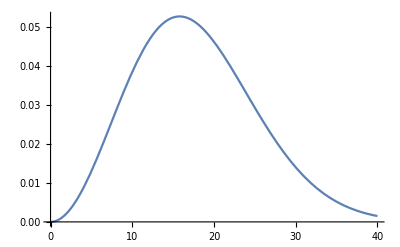

```mathematica
Plot[maxboltz[v,.3],{v,0,40}]
```

This next part generates random velocities along a maxwell-boltzmann distribution.

```mathematica
speedGenMB[n_,T_,vMax_]:=Module[{vList=ConstantArray[0,n],,prob,v,i},
i=1;
While[i≤n,
v=RandomReal[{0,vMax}];
prob=RandomReal[];
If[prob≤maxboltz[v,T],
vList⟦i⟧=v*RotationMatrix[RandomReal[{0,2π}]].{1,0};
i++;
];
];

Return[vList/1000];
]
```

generates a random set of velocities between 0 and 20 m/s (converted to mm/us)

```mathematica
largeSpeedGen[n_]:=Module[{vList={},maxV=20},
vList=Table[{RandomReal[{0,maxV}]RandomChoice[{-1,1}],RandomReal[{0,maxV}]RandomChoice[{-1,1}]},n];
Return[vList/1000]
]
```

```mathematica
velToSim=speedGenMB[20000,.3,40];
```

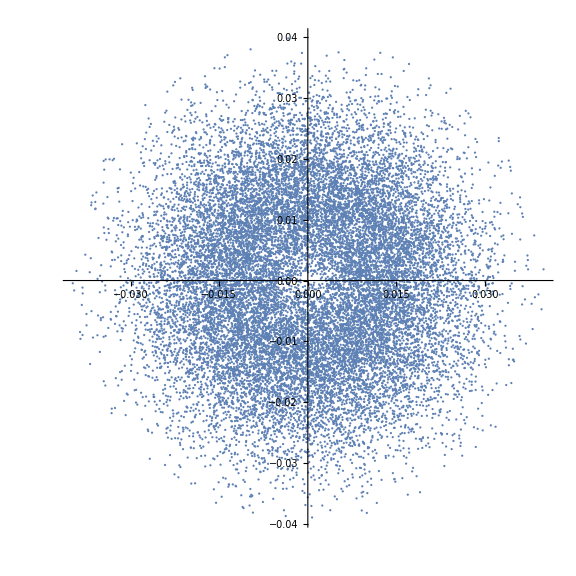

```mathematica
ListPlot[velToSim,AspectRatio->1,ImageSize->Large]
```

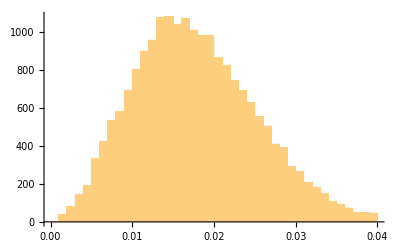

```mathematica
Histogram[Norm/@velToSim,40]
```

Random Position generator

```mathematica
posGen[n_]:=Module[{posList={},randp1,randp2,xMin=.0001,xMax=.0499,yMin=.0001,yMax=.0499,k},
posList=Table[{RandomReal[{xMin,xMax}],RandomReal[{yMin,yMax}]},n];
Return[posList];
]
```

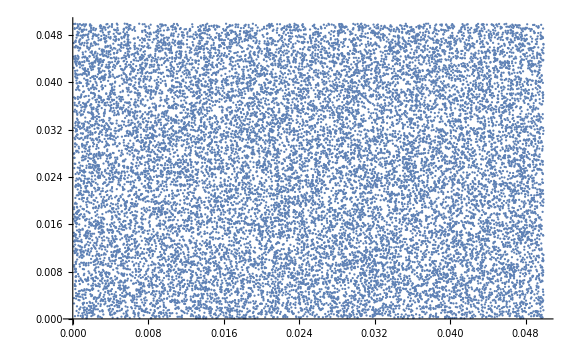

```mathematica
randPositions=posGen[20000];
ListPlot[randPositions,PlotRange->All,ImageSize->Large]
```

```mathematica
Export["positions2Sim.tsv",randPositions];
Export["velocities2Sim.tsv",velToSim];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

Here I just made a Maxwell-Boltzmann distribution in 3-D for fun. The rest is just for fun

```mathematica
Clear[sphericalToCartesian];
sphericalToCartesian[{θ_,ϕ_}]:={Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]};

Clear[randDir];
randDir[]:=Module[{θ,ϕ,vector},
θ=RandomReal[{0,2π}];
ϕ=ArcCos[RandomReal[{-1,1}]];
vector=sphericalToCartesian[{θ,ϕ}];
Return[vector]
]
```

```mathematica
speedGenMB3D[n_,T_,vMax_]:=Module[{vList=ConstantArray[0,n],prob,v,i},
i=1;
While[i≤n,
v=RandomReal[{0,vMax}];
prob=RandomReal[];
If[prob≤maxboltz[v,T],
vList⟦i⟧=v*randDir[];
i++;
];
];

Return[vList/1000];
]
```

```mathematica
testIn3D=speedGenMB3D[10000,.3,40];
```

```mathematica
Histogram3D[velToSim,ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[maxboltz[Norm[{vx,vy}],.3],{vx,-40,40},{vy,-40,40},ImageSize->Large]
```

-Graphics3D-